# LHW 4,5,6: Solution

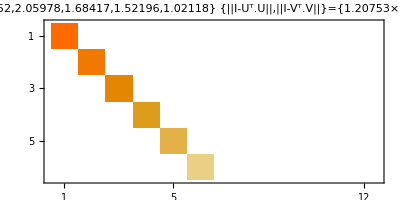

```mathematica
{m,n}={6,12};
A=RandomReal[{-1,1},{m,n}];
{U,S,V}=SingularValueDecomposition[A];
MatrixPlot[S,PlotLabel->
StringForm["σs = ``\n {||I-Uᵀ.U||,||I-Vᵀ.V||}=``",
SingularValueList[A],Map[Norm,{IdentityMatrix[m]-Uᵀ.U,IdentityMatrix[n]-Vᵀ.V}]]]
```

The residual A-U.S.Vᵀ is approximately zero.

```mathematica
Norm[A-U.S.Vᵀ]/Norm[A]
```

8.74837×10^-16

The largest possible value is σ_1 which is given by the first column of V i.e. v_1

The smallest possible value is 0 which is given by any of the last 6 columns of V e.g. v_12

```mathematica
Map[Norm,{A.V⟦All,1⟧,A.V⟦All,12⟧}]
```

{2.46859,4.3995×10^-16}

## Q2

The residuals are appropriately small.

```mathematica
A=RandomReal[{-1,1},{6,6}];
{U,S,V}=SingularValueDecomposition[A];
{λ,X}=Eigensystem[A];X=Xᵀ;
Map[Norm,{A-U.S.Vᵀ,A-X.DiagonalMatrix[λ].Inverse[X]}]
```

{1.7887×10^-15,3.39612×10^-15}

The eigenvalues are not real.

```mathematica
λ
```

{-0.414887+0.877861 ⅈ,-0.414887-0.877861 ⅈ,0.963335,0.43977+0.745665 ⅈ,0.43977-0.745665 ⅈ,-0.667727}

The eigenvectors are not orthogonal.

```mathematica
Norm[ConjugateTranspose[X]-Inverse[X]]
```

1.72555

The largest possible value is σ_1 which is given by the first column of V i.e. v_1

The smallest possible value is σ_6 which is given by any of the last column of V i.e. v_6

```mathematica
TableForm[{Map[Norm,{A.V⟦All,1⟧,A.V⟦All,6⟧}],
SingularValueList[A]⟦{1,6}⟧}]
```

2.33621 | 0.365088
2.33621 | 0.365088

## 5.1

```mathematica
A=RandomReal[{-1,1},{6,6}];
{U,S,V}=SingularValueDecomposition[A];
```

The largest possible value is σ_1 which is given by the first column of V i.e. v_1

The smallest possible value is σ_6 which is given by any of the last column of V i.e. v_6

```mathematica
TableForm[{Map[Norm,{A.V⟦All,1⟧,A.V⟦All,6⟧}],
SingularValueList[A]⟦{1,6}⟧}]
```

2.33621 | 0.365088
2.33621 | 0.365088

Since the smallest singular value is positive A is invertible and A^-1=(U.S.Vᵀ)^-1=V.S^-1.Uᵀ.  In other words all you have to do is reverse the rolls of U and V and take the reciprocals of the singular values on the diagonal of S.

```mathematica
Norm[Inverse[A]-V.Inverse[S].Uᵀ]/Norm[Inverse[A]]
```

1.31769×10^-15

## 5.2

{{12,12},{12,12},{12,12},{12,12}}

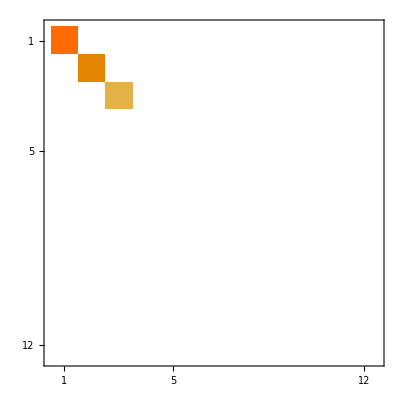

```mathematica
{m,n}={12,3};
{X,Y}=RandomReal[{-1,1},{2,m,n}];
A=X.Yᵀ;
{U,S,V}=SingularValueDecomposition[A];
Map[Dimensions,{A,U,S,V}]
MatrixPlot[S]
```

A is a non-invertible m by m matrix.  S is an mxm square diagonal matrix with only n non-zer0 entries at the top. This is a thick SVD.  The Thin SVD is just the bits needed to reconstruct A.  In this case the first n columns of U and V and the top n×n part of S.

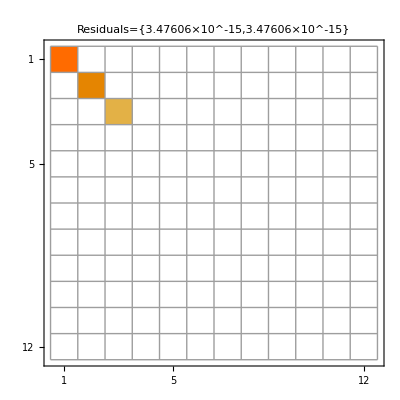

```mathematica
{Ut,St,Vt}={U⟦All,1;;n⟧,S⟦1;;n,1;;n⟧,V⟦All,1;;n⟧};
MatrixPlot[
S,
Mesh->All,
PlotLabel->StringForm["Residuals=``",Map[Norm,{A-U.S.Vᵀ,A-Ut.St.Vtᵀ}]]]
```

The pseudo inverse from our recipe is A^†=Vt.(St)^-1.Utᵀ.  The result is the same as the built in pseudo inverse!

```mathematica
Norm[ PseudoInverse[A]-Vt.Inverse[St].Utᵀ]
```

2.18574×10^-17

## 6.1

The matrix is symmetric and the eigenvalues are real and positive. In other words the matrix is SPD

```mathematica
A=Import[ "https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/bcsstruc1/bcsstk01.mtx.gz"];
{λ,X}=Eigensystem[A];X=Xᵀ;
{Norm[A-Aᵀ],Norm[Im[λ]],Min[λ]}
```

{0.,0,3417.27}

Easy to plot the eigenvalues

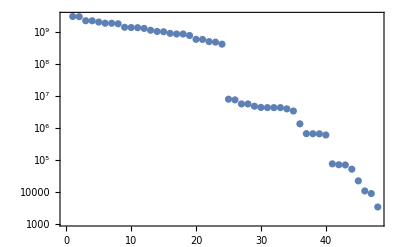

```mathematica
ListLogPlot[λ,GridLines->Automatic,Frame->True]
```

The first pair satisfy the appropriate equation

```mathematica
Norm[A.X⟦All,1⟧-λ⟦1⟧X⟦All,1⟧]
```

2.44181×10^-6

The eigenvectors are orthogonal!

```mathematica
Norm[X.Xᵀ-IdentityMatrix[Length[A]]]
```

5.79343×10^-14

Real symmetric matrices have orthogonal eigenvectors and real eigenvalues.  Absolute values of the eigenvalues are the singular values. Since the eigenvalues are positive the eigenvlues are the singular values.

```mathematica
SingularValueList[A]-Eigenvalues[A]
```

{9.53674×10^-7,-3.8147×10^-6,0.,9.53674×10^-7,3.09944×10^-6,-2.6226×10^-6,-2.38419×10^-6,-1.19209×10^-6,1.19209×10^-6,2.38419×10^-7,7.15256×10^-7,-4.76837×10^-7,7.15256×10^-7,-1.19209×10^-7,-7.15256×10^-7,-4.76837×10^-7,1.19209×10^-6,3.57628×10^-7,-2.38419×10^-7,-4.76837×10^-7,1.66893×10^-6,2.98023×10^-7,2.38419×10^-7,-2.98023×10^-7,1.67638×10^-7,-8.56817×10^-8,-8.75443×10^-8,6.42613×10^-8,2.35625×10^-7,7.35745×10^-8,-1.03377×10^-7,1.58325×10^-8,4.37722×10^-8,-4.42378×10^-8,1.16415×10^-7,-1.02445×10^-8,-9.52277×10^-8,1.8219×10^-7,-9.8953×10^-9,-1.3574×10^-7,-1.74623×10^-9,2.79542×10^-8,6.5731×10^-8,-3.64089×10^-8,-3.80533×10^-8,-1.24559×10^-7,-1.71674×10^-7,-2.09097×10^-8}

### Q5 .2

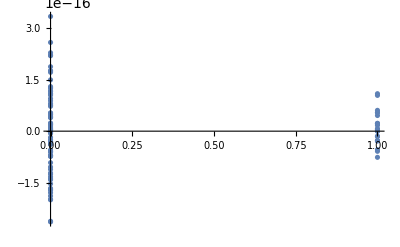

```mathematica
{m,n}={100,23};
A=RandomComplex[{-1-I,1+I},{m,n}];
P=A.Inverse[ConjugateTranspose[A].A].ConjugateTranspose[A];
ListPlot[ReIm[Eigenvalues[P]],PlotRange->All]
```

The m×m H matrix is orthogonal.  The eigenvalues are ±1.

3.3701×10^-15

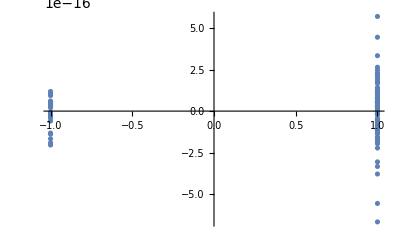

```mathematica
H=IdentityMatrix[m]-2P;
Norm[IdentityMatrix[m]-ConjugateTranspose[H].H]
ListPlot[ReIm[Eigenvalues[H]],PlotRange->All]
```